### Attempt with DSolve

```mathematica
pde=D[u[x,t],t]==d D[u[x,t],{x,2}]-c D[u[x,t],x]
```

u^(0,1)[x,t]==-0.1 u^(1,0)[x,t]+1. u^(2,0)[x,t]

```mathematica
soln=DSolve[{pde,u[x,0]==0,u[0,t]==300,D[u[x,t],x]==0/.x->6},u[x,t],{x,t}]
```

DSolve[{u^(0,1)[x,t]==-0.1 u^(1,0)[x,t]+1. u^(2,0)[x,t],u[x,0]==0,u[0,t]==300,u^(1,0)[6,t]==0},u[x,t],{x,t}]

```mathematica
f[x_,t_]=u[x,t]/.soln[[1]]
```

ReplaceAll::reps: SuperscriptBox[u[x, 0] == 0u[0, t] == 300SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

u[x,t]/.{u^(0,1)[x,t]==-0.1 u^(1,0)[x,t]+1. u^(2,0)[x,t],u[x,0]==0,u[0,t]==300,u^(1,0)[6,t]==0}

### FAIL!

### Attempt using Laplace Transform

```mathematica
pde=D[u[x,t],t]==d D[u[x,t],{x,2}]-c D[u[x,t],x]
```

u^(0,1)[x,t]==-0.1 u^(1,0)[x,t]+1. u^(2,0)[x,t]

```mathematica
ibc={u[x,0]==0,u[0,t]==300,D[u[x,t],x]==0/.x->6}
```

{u[x,0]==0,u[0,t]==300,u^(1,0)[6,t]==0}

```mathematica
teqn=LaplaceTransform[pde,t,s]/.Rule@@@ibc
```

s LaplaceTransform[u[x,t],t,s]==-0.1 LaplaceTransform[u^(1,0)[x,t],t,s]+1. LaplaceTransform[u^(2,0)[x,t],t,s]

```mathematica
tsol=DSolve[teqn/.HoldPattern@LaplaceTransform[a_,t,s]:>a,u[x,t],x]
```

{{u[x,t]→ⅇ^(1/2 (0.1-√(0.01+4. s)) x) C[1]+ⅇ^(1/2 (0.1+√(0.01+4. s)) x) C[2]}}

```mathematica
sol=InverseLaplaceTransform[tsol[[1,1,2]],s,t]//FullSimplify
```

Undefined

### FAIL!

### Attempt using NDSolve

NDSolve attempts to provide an approximate solution with error approximately ≤10^-6.

```mathematica
d=1.0;
c=0.1;
pde=D[u[x,t],t]==d D[u[x,t],{x,2}]-c D[u[x,t],x];
ibc={u[x,0]==0,u[0,t]==300,D[u[x,t],x]==0/.x->6};
```

```mathematica
nsol=NDSolve[{pde,ibc[[1]],ibc[[2]],ibc[[3]]},u[x,t],{x,0,6},{t,0,2}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{u[x,t]→InterpolatingFunction[{{0., 6.}, {0., 2.}}, <>][x,t]}}

A warning is generated because the initial conditions and boundary conditions give two different values for the value of  u(0,0). Essentially, u(x,t) changes instantly at x=0. I can’t fix this at this time.

```mathematica
rowHeadings=Table[x,{x,0,6,0.5}];
columnHeadings={"x","t=0.1","t=0.25","t=0.5","t=1.0","t=2.0"};
TableForm[Evaluate[Transpose[Table[nsol[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}},{x,0,6,0.5}]]],TableHeadings->{rowHeadings,columnHeadings}]
```

| x | t=0.1 | t=0.25 | t=0.5 | t=1.0
0. | 28.5488 | 66.3597 | 118.041 | 189.637 | 259.4
0.5 | 3.48102 | 19.7533 | 53.5799 | 115.152 | 193.106
1. | 0.176926 | 4.21706 | 20.5641 | 64.0021 | 136.933
1.5 | 0.0014624 | 0.619993 | 6.59177 | 32.4515 | 92.4297
2. | -0.0000940839 | 0.0598539 | 1.74485 | 14.9622 | 59.348
2.5 | -3.94259×10^-7 | 0.00350369 | 0.377359 | 6.25409 | 36.2242
3. | 3.37107×10^-8 | 0.0000979055 | 0.065984 | 2.36332 | 21.0042
3.5 | -2.24063×10^-10 | -4.51998×10^-7 | 0.00922396 | 0.805273 | 11.5629
4. | -2.0079×10^-12 | -3.36467×10^-8 | 0.00101609 | 0.246818 | 6.04177
4.5 | 1.9152×10^-13 | 6.36446×10^-9 | 0.0000861397 | 0.0679005 | 3.00147
5. | -2.12979×10^-15 | -1.05665×10^-9 | 5.33448×10^-6 | 0.0167631 | 1.43714
5.5 | -3.15334×10^-17 | -6.71098×10^-11 | 3.02579×10^-7 | 0.0038816 | 0.718653
6. | 1.07814×10^-15 | 6.06648×10^-10 | 8.8691×10^-7 | 0.00166259 | 0.512452

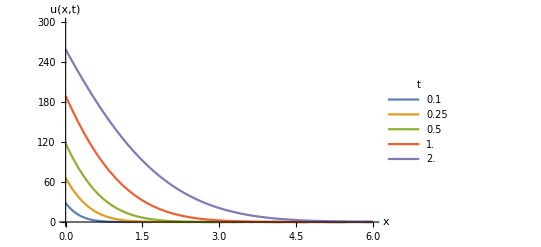

```mathematica
Plot[Evaluate[Table[nsol[[1,1,2]]/.t->a,{a,{0.1,0.25,0.5,1.0,2.0}}]],{x,0,6},PlotLegends->LineLegend[{0.1,0.25,0.5,1.0,2.0},LegendLabel->t],PlotRange->{0,300},AxesLabel->{x,u[x,t]}]
```

### SUCCESS (I think)!

Equation 1

```mathematica
dt= .1
```

0.1

```mathematica
uN[j_,m_]:=uN[j, m-1]+(c*dt)/(2*dx)(uN[j+1,m-1]-uN[j-1,m-1])+(d*dt)/dx^2(uN[j+1,m-1]-2uN[j,m-1]+u[j-1,m-1])
```

```mathematica
uN[0,m_]=uN
```

```mathematica
ibc={uN[x,0]==0,uN[0,t]==300,D[uN[x,t],x]==0/.x->6};
```